```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomi/Dropbox (Cambridge University)/Physics/SimulationsLSC/Example_simulation/yb/Raytracing

```mathematica
files=FileNames["*","./side_emission/"<>ToString[#]]&/@Range[300,480];
nums=ToExpression[StringDrop[#,20]]&/@files;
```

```mathematica
Sort[nums[[1]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89}

```mathematica
datatable=Table[{wavelength+300-1,angle,If[ContainsAny[nums[[wavelength]],{angle}]==True,1,0]},{wavelength,1,180,1},{angle,1,91,1}];
```

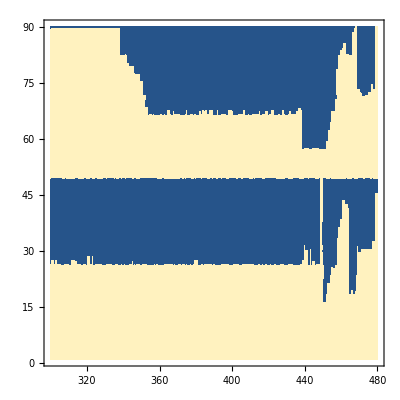

```mathematica
ListDensityPlot[Flatten[datatable,1],InterpolationOrder->0,PlotRange->{{300,480},{1,90}}]
```

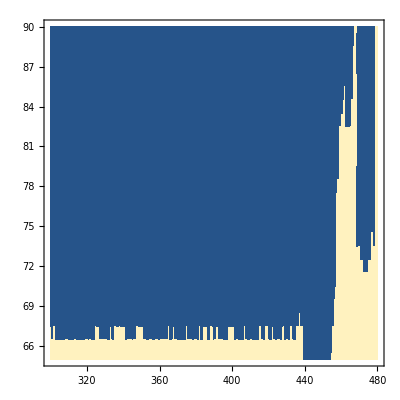

```mathematica
ListDensityPlot[Flatten[datatable,1],InterpolationOrder->0,PlotRange->{{300,480},{65,90}}]
```